## IPE Beam + Refinement

```mathematica
h=100; b=55; r=7; tf=5.7; tw=4.1 ; n=1000; (*n denotes the curve refinement*)
```

## Coordinates

```mathematica
Viertelkreis1=N[CirclePoints[{(b-tw)/2-r,tf+r},r,4n][[2;;n]]];
Viertelkreis2=N[CirclePoints[{(b-tw)/2-r,h-tf-r},r,4n][[n+2;;2n]]];
Viertelkreis3=N[CirclePoints[{(b+tw)/2+r,h-tf-r},r,4n][[2n+2;;3n]]];
Viertelkreis4=N[CirclePoints[{(b+tw)/2+r,tf+r},r,4n][[3n+2;;4n]]];

nodes={{0,0},{0,tf},{(b-tw)/2-r,tf},Viertelkreis1,{(b-tw)/2,tf+r},{(b-tw)/2,h-r-tf},Viertelkreis2, {(b-tw)/2-r,h-tf},{0,h-tf},{0,h},{b,h},{b,h-tf},{(b+tw)/2+r,h-tf},Viertelkreis3,{(b+tw)/2,h-tf-r},{(b+tw)/2,tf+r},Viertelkreis4,{(b+tw)/2+r,tf},{b,tf},{b,0}};
coor=Partition[Flatten[nodes],2];
```

## Mesh

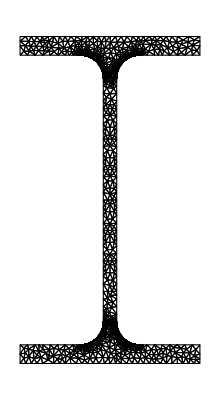

```mathematica
<<NDSolve`FEM`;
mesh=ToElementMesh[Polygon[coor]
,"MeshOrder"-> 1
,MaxCellMeasure->2 (*Reduce this value for a more refined mesh*)
];
belmt=mesh["BoundaryElements"]⟦1,1⟧;
XI=mesh["Coordinates"];
elmt=mesh["MeshElements"]⟦1,1⟧;
mesh["Wireframe"]
```

## Geommetry

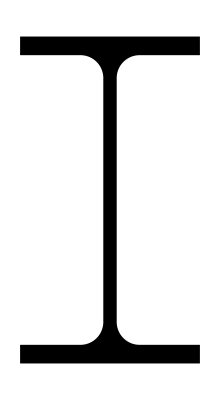

-Graphics-

```mathematica
Graphics[Polygon[coor]]
Graphics[
GraphicsComplex[
XI,
{
{PointSize->Medium,Red,Point[Range[XI//Length]]},
{FaceForm[LightBlue],EdgeForm[Black],Polygon[elmt]},
{Green,Line[belmt]},
{Blue,Arrow[belmt]}
}
]
]
```